```mathematica
Quit[];
```

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.11 (2 Sep 2019)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (6 Oct 2019)

by Thomas Hahn

```mathematica
(* Create my topologies. *)
(* 0 loops, 2 incoming legs, 2 outgoing legs.*)
topologies=CreateTopologies[0,2 -> 2];
_Hel=0;
Print[topologies];
```

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

in total: 1 Classes insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

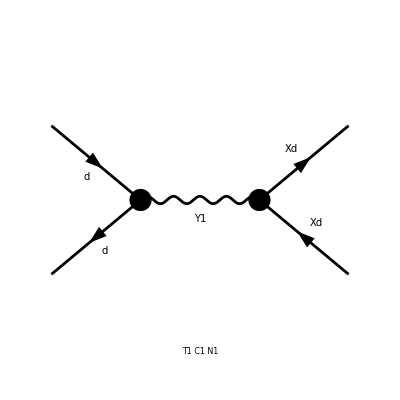

```mathematica
(* ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]} *)
diag=InsertFields[topologies,{F[10,{1}],-F[10,{1}]}->{F[13],-F[13]},InsertionLevel->{Classes},
Model->"DMsimp_s_spin1_FeynmanGauge",
GenericModel->"DMsimp_s_spin1_FeynmanGauge"];
Paint[diag];
```

```mathematica
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/kpachal/fc-amp-1.frm

running FORM...

ok